```mathematica
SetDirectory[NotebookDirectory[]];
$Assumptions=l∈ Integers&& m ∈Integers&&l>m&&l>10&&m>10&&f[r]>0&&l-m>8;
```

```mathematica
<<"Il_result.mx";(*Il*)
<<"Il0_result.mx";(*Il0*)
<<"CiMuNu_result.mx";(*CiMuNu*)
<<"clTPhi_result.mx";(*clTPhi*)
<<"csT_result.mx";(*csTPsi*)
```

```mathematica
Subscript[Φ, l_,m_] :=2 √(π/(2l+1)) ⅇ^(ⅈ m ((r0 ur ℒ Δr)/((-2 M+r0) (r0^2+ℒ^2))-ϕ0)) WignerD[{l,m,0},π,π/2,π/2] * Il0;
Subscript[ψ, l_,m_]:=2 √(π/(2l+1))ⅇ^(ⅈ m ((r0 ur ℒ Δr)/((-2 M+r0) (r0^2+ℒ^2))-ϕ0)) WignerD[{l,m,0},π,π/2,π/2];
```

```mathematica
Subscript[psi, l,m] = Flatten[Il/.{e->ℰ,L->ℒ}]*Subscript[ψ, l,m]//Expand//Simplify;
rulePsi1 = Thread[(Subscript[#,i_,j_]&/@ToExpression["ψ"<>ToString[#]&/@Range[6]])->Subscript[psi, l,m]];
```

```mathematica
term1 = csTPsi/.rulePsi1;
hMuNulm=clTPhi+term1;
```

```mathematica
hMuNulpmp[l_,m_]=hMuNulm;
```

## 计算1

```mathematica
Δrlists=Range[-0.1,0.1,0.01];
Mvalue=1;
r0value=10;
ϕ0value=Pi/6;
pv=10;
ev=1/7;
ℰvalue=Sqrt[((pv-2-2ev)(pv-2+2ev))/(pv(pv-3-ev^2))];
ℒvalue=pv/Sqrt[pv-3-ev^2];

utvalue=ℰvalue/(1-2/r0value);
urvalue=√(ℰvalue^2+((2 M-r0value) (ℒvalue^2+r0value^2))/r0value^3);
uϕvalue=ℒvalue/r0value^2;
kvalue = ℒvalue^2/(r0value^2+ℒvalue^2);
```

```mathematica
lvalue=2;
mvalue=2;
cvalue = (r0value ℒvalue urvalue)/((r0value-2Mvalue)(r0value^2+ℒvalue^2))Δr;
parametersvalue={l->lvalue,m->mvalue,r0->r0value,ϕ0->ϕ0value,ℰ->ℰvalue,ℒ->ℒvalue,r0->r0value,ϕ0->ϕ0value,ur->urvalue,ut->utvalue,uϕ->uϕvalue,M->Mvalue,c->cvalue,r->r0value+Δr,k->kvalue};
```

```mathematica
Total[CiMuNu[[1]]*hMuNulpmp[lp,mp]]
```

$Aborted

```mathematica
Sum[hMuNulpmp[lp,mp][[1,1]]*KroneckerDelta[l,lp],{lp,-Infinity,Infinity}]
```

$Aborted

```mathematica
CiMuNu[[1]][[2,2]]
```

((√(((-3+l-m) (-2+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))))/(4 √2)-(√(((-3+l-m) (-2+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) M)/(2 √2 r)) -2+l,lp 2+m,mp+(-(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) √(((1+l+m) (2+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))))/(4 √2)-(√(((-1+l-m) (l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))))/(4 √2)+(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) √(((1+l+m) (2+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) M)/(2 √2 r)+(√(((-1+l-m) (l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) M)/(2 √2 r)) l,lp 2+m,mp+((√(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) √(((3+l+m) (4+l+m))/((1+2 (1+l)) (3+2 (1+l)))))/(4 √2)-(√(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) √(((3+l+m) (4+l+m))/((1+2 (1+l)) (3+2 (1+l)))) M)/(2 √2 r)) 2+l,lp 2+m,mp

```mathematica
(*用法：FastDeltaContract[表达式,{求和指标1,求和指标2...}] 功能：自动寻找包含求和指标的 KroneckerDelta，解出关系并代入*)FastDeltaContract[expr_,vars_List]:=Module[{res=expr,foundRule},Scan[Function[v,(*循环直到没有包含 v 的 Delta 为止*)FixedPoint[(Replace[#,{(*匹配形式：任意项*Delta[A,B]*)(*Condition/;!FreeQ[{A,B},v] 确保 Delta 里包含求和指标*)Times[coeff___,KroneckerDelta[A_,B_],rest___]/;!FreeQ[{A,B},v]:>Module[{sol,target},(*尝试解线性方程 A==B，求解 v*)sol=Solve[A==B,v];
If[sol=!={}&&Length[sol]==1,(*如果解出来了，执行替换*)(Times[coeff,rest]/. sol[[1]]),(*如果解不出来，保持原样*)Times[coeff,KroneckerDelta[A,B],rest]]]},{0,Infinity}] (*在所有层级搜索*))&,res]],vars];
res]

(*为了方便单变量调用*)
FastDeltaContract[expr_,v_Symbol]:=FastDeltaContract[expr,{v}];
```

### KroneckerDelta函数规则

```mathematica
(* ============================================================
   FastDeltaContract
   ------------------------------------------------------------
   用法:
     FastDeltaContract[expr, i]                 (* 单个求和指标 *)
     FastDeltaContract[expr, {i, k, ...}]       (* 多个求和指标 *)

   功能:
     在 expr 中寻找包含求和指标 v 的 KroneckerDelta[a,b]，
     从方程 a == b 中解出 v（优先处理 v±常数 等仿射形式），
     然后:
       1) 删除该 KroneckerDelta
       2) 把解出的 v -> (...) 代回该乘积剩余部分
     并重复该过程直到无法继续（对每个 v 分别做完再换下一个）。

   性能点:
     - 对 KroneckerDelta[v+1, j] 这类常见情况不调用 Solve
     - 用 ReplaceRepeated 带迭代上限避免死循环
     - Simplify 是可选的（可换成 Identity 进一步提速）
   ============================================================ *)

ClearAll[
  FastDeltaContract,            (* 主函数 *)
  deltaContractRule,            (* 为单个指标 v 构造收缩替换规则 *)
  deltaSolveRuleAffine          (* 从 a==b 里尝试解出 v 的快速求解器 *)
];

(* ---------------------------
   Options: 给用户的可配置项
   --------------------------- *)
Options[FastDeltaContract] = {
  Assumptions -> True,          (* 传给 Simplify / Solve 的额外假设 *)
  Domain -> Integers,           (* Solve 时约束 v 属于哪个域（常见为 Integers） *)
  FallbackSolve -> False,       (* 快速规则失败时，是否启用 Solve 兜底 *)
  AllowNonUnitCoefficient -> False,  (* 是否允许 (k v + c) 这类 k≠±1 的线性解 *)
  MaxIterations -> 200,         (* ReplaceRepeated 的迭代上限，防止极端情况卡住 *)
  SimplifyFunction -> Automatic (* 简化函数：Automatic=用 Simplify[...,Assumptions]；
                                   也可设 Identity 或自定义纯函数 *)
};

(* ============================================================
   入口 1：单变量版本
   ------------------------------------------------------------
   作用：把 FastDeltaContract[expr, i] 转成列表版本，避免重复代码
   ============================================================ *)
FastDeltaContract[expr_, v_Symbol, opts : OptionsPattern[]] :=
  FastDeltaContract[expr, {v}, opts];

(* ============================================================
   入口 2：多变量版本（核心调度）
   ============================================================ *)
FastDeltaContract[expr_, vars_List, opts : OptionsPattern[]] := Module[
  {
    (* 从 Options 中取值：OptionValue 会读取用户传入的 opts 或默认值 *)
    ass = OptionValue[Assumptions],
    dom = OptionValue[Domain],
    fb  = OptionValue[FallbackSolve],
    allowNonUnit = OptionValue[AllowNonUnitCoefficient],
    maxIt = OptionValue[MaxIterations],
    simpOpt = OptionValue[SimplifyFunction],

    (* simp 是最终使用的“简化函数”，做成一元函数 simp[x] *)
    simp
  },

  (* 选择简化函数：默认用 Simplify[x, ass]，也允许用户传 Identity 或自定义 *)
  simp = Which[
    simpOpt === Automatic,
      Function[x, Simplify[x, ass]],      (* Automatic：带 Assumptions 的 Simplify *)

    Head[simpOpt] === Function,
      simpOpt,                            (* 用户自己给了纯函数 *)

    simpOpt === Identity,
      Identity,                           (* 完全不简化：最快 *)

    True,
      (* 其它情况：尽量当作“单参函数符号”调用，比如 FullSimplify / Simplify *)
      Function[x, simpOpt[x]]
  ];

  (* Fold 的作用：对 vars 逐个处理
     - 初始累积值是 expr
     - 对每个 v，把当前表达式 e 做一次“对 v 的 delta 收缩”
   *)
  Fold[
    Function[{e, v},
      (* ReplaceRepeated[e, rule, maxIt]：
         重复应用 rule 直到稳定或达到 maxIt 次。
         这是 “//.” 的更可控版本（多了迭代上限）。
      *)
   ReplaceRepeated[e,deltaContractRule[v,ass,dom,fb,allowNonUnit,simp],MaxIterations->maxIt]
    ],
    expr,
    vars
  ]
];

(* ============================================================
   deltaContractRule：为单个求和指标 v 构造“收缩规则”
   ------------------------------------------------------------
   输入:
     v          要消去的求和指标
     ass/dom/... 选项参数
     simp       简化函数（已在主函数里准备好）
   输出:
     一个替换规则（RuleDelayed 形式），用于 ReplaceRepeated
   ============================================================ *)
deltaContractRule[v_, ass_, dom_, fb_, allowNonUnit_, simp_] :=
  (
    (* HoldPattern：防止匹配时被 Mathematica 先行改写/求值
       我们要匹配的是“乘积里有一个 KroneckerDelta[a,b]”
     *)
    HoldPattern[
      Times[pre___, KroneckerDelta[a_, b_], post___]
    ]
    /; !FreeQ[{a, b}, v]               (* 条件：a 或 b 里必须出现 v，否则不处理 *)
    :>
      Module[{rep, candidate},
        (* 尝试从 a==b 中解出 v，返回 {v -> ...} 或 None *)
        rep = deltaSolveRuleAffine[a, b, v, ass, dom, fb, allowNonUnit, simp];

        If[rep === None,
          (* 解不出来：保持原式不变 *)
          Times[pre, KroneckerDelta[a, b], post],

          (* 解出来：删除 delta，并把 v 替换到剩余因子上 *)
          candidate = (Times[pre, post] /. rep);

          (* 额外安全：如果替换后仍然含 v，说明这次替换不靠谱（会导致循环/错误）
             这种情况下宁可不动。
           *)
          If[FreeQ[candidate, v],
            candidate,
            Times[pre, KroneckerDelta[a, b], post]
          ]
        ]
      ]
  );

(* ============================================================
   deltaSolveRuleAffine：快速从 KroneckerDelta[a,b] 的 a==b 解出 v
   ------------------------------------------------------------
   优先级:
     1) 直接模式匹配：v±c、-v+c（最快，覆盖 i+1,j 等）
     2) 一般一次多项式：a-b = c1 v + c0（可选允许 c1≠±1）
     3) 兜底 Solve（默认关闭）
   返回:
     - {v -> expr}   （唯一替换）
     - None          （不替换）
   ============================================================ *)
deltaSolveRuleAffine[a_, b_, v_, ass_, dom_, fb_, allowNonUnit_, simp_] := Module[
  {rep, eq, c1, c0, sol, rhs, c, candidate},

  (* ---------------------------
     1) 最快路径：直接仿射匹配
     ---------------------------
     这里用 Replace 在 {a,b} 上做一次匹配，命中就直接构造 v -> ...
     关键点：
       - FreeQ[c, v]：偏移量 c 不能含 v
       - rhs 可以含其它指标（如 j,k...）
  *)
  rep = Replace[
    {a, b},
    {
      (* a 形如 v + c ： v == rhs - c *)
      {v + c_. , rhs_} /; FreeQ[c, v] :>
        With[{cand = rhs - c}, If[FreeQ[cand, v], {v -> simp[cand]}, None]],

      (* a 形如 v - c ： v == rhs + c *)
      {v - c_. , rhs_} /; FreeQ[c, v] :>
        With[{cand = rhs + c}, If[FreeQ[cand, v], {v -> simp[cand]}, None]],

      (* a 形如 -v + c ： -v + c == rhs -> v == c - rhs *)
      {-v + c_. , rhs_} /; FreeQ[c, v] :>
        With[{cand = c - rhs}, If[FreeQ[cand, v], {v -> simp[cand]}, None]],

      (* b 在左边同理（对称处理） *)
      {rhs_, v + c_.} /; FreeQ[c, v] :>
        With[{cand = rhs - c}, If[FreeQ[cand, v], {v -> simp[cand]}, None]],

      {rhs_, v - c_.} /; FreeQ[c, v] :>
        With[{cand = rhs + c}, If[FreeQ[cand, v], {v -> simp[cand]}, None]],

      {rhs_, -v + c_.} /; FreeQ[c, v] :>
        With[{cand = c - rhs}, If[FreeQ[cand, v], {v -> simp[cand]}, None]]
    },
    {0}  (* levelspec：只对整体 {a,b} 做一次替换 *)
  ];

  (* 如果 rep 得到了形如 {v -> something} 的规则，就立刻返回 *)
  If[MatchQ[rep, {v -> _}], Return[rep]];

  (* ---------------------------
     2) 一般线性路径：a-b 对 v 是一次多项式
     ---------------------------
     思路：
       eq = Expand[a-b]
       若 eq = c1 v + c0，则 v -> -c0/c1
     注意：
       - 这一步更通用，但也更容易引入 “非整数/整除条件”
       - 默认只允许 c1 = ±1（更符合整数指标收缩的直觉）
  *)
  eq = Expand[a - b];

  If[PolynomialQ[eq, v] && Exponent[eq, v] == 1,
    c1 = Coefficient[eq, v];          (* v 的系数 *)
    c0 = simp[eq /. v -> 0];          (* 常数项：把 v 设 0 即可取出 *)

    (* 系数必须不为 0，且不含 v（避免非线性/奇怪依赖） *)
    If[c1 =!= 0 && FreeQ[c1, v],
      If[allowNonUnit || c1 === 1 || c1 === -1,
        candidate = simp[-c0/c1];
        If[FreeQ[candidate, v],
          Return[{v -> candidate}],
          Return[None]
        ],
        (* 默认更安全：k≠±1 不做收缩 *)
        Return[None]
      ]
    ];
  ];

  (* ---------------------------
     3) 兜底 Solve（默认关闭）
     ---------------------------
     只有用户显式设置 FallbackSolve->True 才走到这里。
     Solve 可能慢，也可能产生多解/带条件解，我们只接受“唯一解”。
  *)
  If[TrueQ[fb],
    sol = Solve[
      a == b,
      v,
      Assumptions -> (ass && Element[v, dom])
    ];
    If[Length[sol] == 1, sol[[1]], None],
    None
  ]
];
```

```mathematica
FastDeltaContract[Expand[hh[lp,mp]*CiMuNu[[1,2,2]]],{lp,mp}]
```

(√(((-3+l-m) (-2+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) hh[-2+l,2+m])/(4 √2)-(√(((-3+l-m) (-2+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) M hh[-2+l,2+m])/(2 √2 r)-(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) √(((1+l+m) (2+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) hh[l,2+m])/(4 √2)-(√(((-1+l-m) (l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) hh[l,2+m])/(4 √2)+(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) √(((1+l+m) (2+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) M hh[l,2+m])/(2 √2 r)+(√(((-1+l-m) (l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) M hh[l,2+m])/(2 √2 r)+(√(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) √(((3+l+m) (4+l+m))/((1+2 (1+l)) (3+2 (1+l)))) hh[2+l,2+m])/(4 √2)-(√(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) √(((3+l+m) (4+l+m))/((1+2 (1+l)) (3+2 (1+l)))) M hh[2+l,2+m])/(2 √2 r)

```mathematica
CiMuNu[[1,2,2]]
```

((√(((-3+l-m) (-2+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))))/(4 √2)-(√(((-3+l-m) (-2+l-m))/((-1+2 (-1+l)) (1+2 (-1+l)))) √(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) M)/(2 √2 r)) -2+l,lp 2+m,mp+(-(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) √(((1+l+m) (2+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))))/(4 √2)-(√(((-1+l-m) (l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))))/(4 √2)+(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) √(((1+l+m) (2+l+m))/((1+2 (-1+l)) (3+2 (-1+l)))) M)/(2 √2 r)+(√(((-1+l-m) (l-m))/((-1+2 (1+l)) (1+2 (1+l)))) √(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) M)/(2 √2 r)) l,lp 2+m,mp+((√(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) √(((3+l+m) (4+l+m))/((1+2 (1+l)) (3+2 (1+l)))))/(4 √2)-(√(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) √(((3+l+m) (4+l+m))/((1+2 (1+l)) (3+2 (1+l)))) M)/(2 √2 r)) 2+l,lp 2+m,mp

```mathematica
(* ============================================================FastDeltaContract 线性补丁 (Linearity Patch)------------------------------------------------------------ 功能:让函数自动处理 Sum (Plus) 和 Scalar*Sum 的情况，无需用户手动 Expand 或 Distribute。
============================================================*)(*1. 对加法的线性支持：F[a+b]=F[a]+F[b]*)FastDeltaContract[expr_Plus,vars_List,opts:OptionsPattern[]]:=FastDeltaContract[#,vars,opts]&/@expr;

(*2. 对乘积中包含加法的自动分配：F[a*(b+c)]->F[a*b+a*c] 注意：这里只针对含有 Plus 的 Times 进行 Distribute，非常克制且高效*)
FastDeltaContract[expr_Times,vars_List,opts:OptionsPattern[]]:=Module[{distributed},(*检查乘积里是否有加法结构*)If[Not@FreeQ[expr,Plus],(*如果有，只做这一层的分配律，不做深度 Expand*)distributed=Distribute[expr];
(*如果分配后结构变了（确实拆开了括号），就递归调用处理拆开后的结果*)If[distributed=!=expr,FastDeltaContract[distributed,vars,opts],(*否则（防止死循环），进入原来的核心逻辑*)FastDeltaContractCore[expr,vars,opts]],(*如果没有加法，直接进入核心逻辑*)FastDeltaContractCore[expr,vars,opts]]];

(* ============================================================重要步骤：重命名原来的主函数------------------------------------------------------------ 我们需要把之前定义的 FastDeltaContract[expr_,vars_List...] 改名为 FastDeltaContractCore，以便上面的拦截代码能调用它。请务必重新运行下面这段修改后的核心模块：
============================================================*)

(*这一步覆盖之前的 Module 定义*)
FastDeltaContractCore[expr_,vars_List,opts:OptionsPattern[]]:=Module[{ass=OptionValue[FastDeltaContract,Assumptions],(*注意取值来源*)dom=OptionValue[FastDeltaContract,Domain],fb=OptionValue[FastDeltaContract,FallbackSolve],allowNonUnit=OptionValue[FastDeltaContract,AllowNonUnitCoefficient],maxIt=OptionValue[FastDeltaContract,MaxIterations],simpOpt=OptionValue[FastDeltaContract,SimplifyFunction],simp},simp=Which[simpOpt===Automatic,Function[x,Simplify[x,ass]],simpOpt===Identity,Identity,Head[simpOpt]===Function,simpOpt,True,Function[x,simpOpt[x]]];
Fold[Function[{e,v},ReplaceRepeated[e,deltaContractRule[v,ass,dom,fb,allowNonUnit,simp],MaxIterations->maxIt]],expr,vars]];

(*最后的兜底：如果没有触发 Plus/Times 规则，直接调 Core*)
FastDeltaContract[expr_,vars_List,opts:OptionsPattern[]]:=FastDeltaContractCore[expr,vars,opts];
```

```mathematica
Factor[FastDeltaContract[Expand[hh[lp,mp]*CiMuNu[[1,2,2]]],{lp,mp}]]
```

-1/(4 √2 r)(2 M-r) (√((-l+l^2+m-2 l m+m^2)/(-1+4 l^2)) √((6-5 l+l^2+5 m-2 l m+m^2)/(3-8 l+4 l^2)) hh[-2+l,2+m]-√((-l+l^2+m-2 l m+m^2)/(-1+4 l^2)) √((2+3 l+l^2+3 m+2 l m+m^2)/(-1+4 l^2)) hh[l,2+m]-√((-l+l^2+m-2 l m+m^2)/(3+8 l+4 l^2)) √((2+3 l+l^2+3 m+2 l m+m^2)/(3+8 l+4 l^2)) hh[l,2+m]+√((2+3 l+l^2+3 m+2 l m+m^2)/(3+8 l+4 l^2)) √((12+7 l+l^2+7 m+2 l m+m^2)/(15+16 l+4 l^2)) hh[2+l,2+m])

```mathematica
(* ============================================================FastDeltaContract 列表补丁 (Listability Patch)------------------------------------------------------------ 功能:让函数自动“穿透”列表/矩阵。当输入是 List 时，自动对 List 的每个元素递归调用自身。
============================================================*)FastDeltaContract[expr_List,vars_List,opts:OptionsPattern[]]:=FastDeltaContract[#,vars,opts]&/@expr;
```

```mathematica
symbolicHi=Table[hCell[i,j,lp,mp],{i,4},{j,4}];
expr1 = symbolicHi*CiMuNu[[2]];
contracted = FastDeltaContract[expr1,{lp,mp}]
```

{{0,(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) hCell[1,2,-1+l,1+m])/(2 √2)-(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) M hCell[1,2,-1+l,1+m])/(√2 r)-(√(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) hCell[1,2,1+l,1+m])/(2 √2)+(√(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) M hCell[1,2,1+l,1+m])/(√2 r),-(√(((-1+l+m) (l+m))/((-1+2 l) (1+2 l))) hCell[1,3,-1+l,-1+m])/(2 √2)+(√(((-1+l+m) (l+m))/((-1+2 l) (1+2 l))) M hCell[1,3,-1+l,-1+m])/(√2 r)+(√(((1+l-m) (2+l-m))/((1+2 l) (3+2 l))) hCell[1,3,1+l,-1+m])/(2 √2)-(√(((1+l-m) (2+l-m))/((1+2 l) (3+2 l))) M hCell[1,3,1+l,-1+m])/(√2 r),(√(((l-m) (l+m))/((-1+2 l) (1+2 l))) hCell[1,4,-1+l,m])/(√2)-(√2 √(((l-m) (l+m))/((-1+2 l) (1+2 l))) M hCell[1,4,-1+l,m])/r+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) hCell[1,4,1+l,m])/(√2)-(√2 √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) M hCell[1,4,1+l,m])/r},{(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) hCell[2,1,-1+l,1+m])/(2 √2)-(√(((-1+l-m) (l-m))/((-1+2 l) (1+2 l))) M hCell[2,1,-1+l,1+m])/(√2 r)-(√(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) hCell[2,1,1+l,1+m])/(2 √2)+(√(((1+l+m) (2+l+m))/((1+2 l) (3+2 l))) M hCell[2,1,1+l,1+m])/(√2 r),0,0,0},{-(√(((-1+l+m) (l+m))/((-1+2 l) (1+2 l))) hCell[3,1,-1+l,-1+m])/(2 √2)+(√(((-1+l+m) (l+m))/((-1+2 l) (1+2 l))) M hCell[3,1,-1+l,-1+m])/(√2 r)+(√(((1+l-m) (2+l-m))/((1+2 l) (3+2 l))) hCell[3,1,1+l,-1+m])/(2 √2)-(√(((1+l-m) (2+l-m))/((1+2 l) (3+2 l))) M hCell[3,1,1+l,-1+m])/(√2 r),0,0,0},{(√(((l-m) (l+m))/((-1+2 l) (1+2 l))) hCell[4,1,-1+l,m])/(√2)-(√2 √(((l-m) (l+m))/((-1+2 l) (1+2 l))) M hCell[4,1,-1+l,m])/r+(√(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) hCell[4,1,1+l,m])/(√2)-(√2 √(((1+l-m) (1+l+m))/((1+2 l) (3+2 l))) M hCell[4,1,1+l,m])/r,0,0,0}}

```mathematica
finalResult = contracted/.hCell[i_,j_,newL_,newM_]:>(hMuNulpmp[newL,newM][[i,j]]);
```

```mathematica
h2lm = Total[finalResult,All];
```

```mathematica
h2lm
```

```mathematica
k
```

k

```mathematica
result1 = Re[N[r/(√2) h2lm/.parametersvalue/.{Δr->Δrlists,M->1,B[i_,j_]->Beta[i,j],F[i_,j_,k_,l_]->Hypergeometric2F1[i,j,k,l]}]]
```

{7.00036 (-0.000529145+0.134883 (0.0675334+Re[(1.40433-20.9047 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(72.1757+6.91539 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.5224 (0.135192+Re[(2.32793+34.6533 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(119.644-11.4635 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.504687 (-0.108921+Re[(143.133+13.7141 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.78496-41.4566 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.00743 (-0.00053139+0.134918 (0.0678608+Re[(1.40637-20.9527 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(72.4312+6.93117 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.522534 (0.135777+Re[(2.33132+34.7328 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(120.068-11.4897 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.504816 (-0.109125+Re[(143.64+13.7454 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.78901-41.5517 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.0145 (-0.000533636+0.134952 (0.0681882+Re[(1.40842-21.0007 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(72.6872+6.94697 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.522667 (0.13636+Re[(2.3347+34.8124 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(120.492-11.5158 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.504944 (-0.109327+Re[(144.148+13.7767 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.79306-41.6469 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.02157 (-0.000535883+0.134986 (0.0685157+Re[(1.41046-21.0488 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(72.944+6.96279 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.5228 (0.136941+Re[(2.33809+34.8921 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(120.918-11.5421 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.505073 (-0.109529+Re[(144.657+13.8081 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.79712-41.7423 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.02864 (-0.000538131+0.135021 (0.0688432+Re[(1.41251-21.0969 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(73.2014+6.97864 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.522933 (0.13752+Re[(2.34148+34.9719 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(121.344-11.5683 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.505201 (-0.109729+Re[(145.167+13.8395 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.80118-41.8378 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.03571 (-0.00054038+0.135055 (0.0691707+Re[(1.41456-21.1452 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(73.4594+6.9945 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.523065 (0.138099+Re[(2.34488+35.0519 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(121.772-11.5946 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.505329 (-0.109928+Re[(145.679+13.8709 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.80524-41.9334 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.04278 (-0.00054263+0.135089 (0.0694982+Re[(1.41661-21.1934 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(73.7181+7.01039 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.523197 (0.138675+Re[(2.34828+35.1319 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(122.201-11.621 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.505456 (-0.110126+Re[(146.192+13.9024 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.8093-42.0292 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.04985 (-0.000544881+0.135123 (0.0698257+Re[(1.41866-21.2418 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(73.9775+7.02629 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.523329 (0.13925+Re[(2.35168+35.2121 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(122.631-11.6473 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.505584 (-0.110322+Re[(146.706+13.934 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.81338-42.1251 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.05693 (-0.000547133+0.135157 (0.0701533+Re[(1.42071-21.2902 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(74.2375+7.04222 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.523461 (0.139823+Re[(2.35509+35.2924 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(123.062-11.6737 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.505711 (-0.110518+Re[(147.222+13.9656 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.81745-42.2211 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.064 (-0.000549386+0.135191 (0.0704808+Re[(1.42277-21.3387 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(74.4982+7.05817 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.523592 (0.140394+Re[(2.3585+35.3727 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(123.494-11.7002 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.505838 (-0.110712+Re[(147.739+13.9972 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.82153-42.3173 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.07107 (-0.00055164+0.135225 (0.0708083+Re[(1.42483-21.3873 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(74.7596+7.07413 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.523723 (0.140964+Re[(2.36191+35.4532 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(123.927-11.7266 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.505964 (-0.110905+Re[(148.257+14.0289 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.82561-42.4136 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.07814 (-0.000549714+0.135258 (0.0705992+Re[(1.42689-21.4359 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(75.0216+7.09012 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.523854 (0.140464+Re[(2.36532+35.5339 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(124.362-11.7531 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.506091 (-0.110738+Re[(148.777+14.0606 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.82969-42.51 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.08521 (-0.000547788+0.135292 (0.0703896+Re[(1.42895-21.4846 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(75.2842+7.10613 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.523984 (0.139964+Re[(2.36874+35.6146 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(124.797-11.7797 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.506217 (-0.110569+Re[(149.298+14.0923 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.83378-42.6066 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.09228 (-0.000545859+0.135326 (0.0701794+Re[(1.43101-21.5334 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(75.5476+7.12216 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.524115 (0.139464+Re[(2.37216+35.6954 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(125.234-11.8063 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.506343 (-0.1104+Re[(149.82+14.1241 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.83788-42.7033 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.09935 (-0.000543929+0.135359 (0.0699687+Re[(1.43308-21.5822 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(75.8116+7.13821 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.524245 (0.138963+Re[(2.37559+35.7764 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(125.671-11.8329 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.506468 (-0.110231+Re[(150.344+14.1559 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.84197-42.8002 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.10642 (-0.000541998+0.135393 (0.0697575+Re[(1.43515-21.6311 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(76.0763+7.15429 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.524374 (0.138462+Re[(2.37901+35.8574 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(126.11-11.8595 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.506594 (-0.110061+Re[(150.869+14.1878 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.84607-42.8971 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.11349 (-0.000540065+0.135426 (0.0695458+Re[(1.43722-21.6801 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(76.3416+7.17038 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.524504 (0.137961+Re[(2.38245+35.9386 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(126.55-11.8862 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.506719 (-0.109891+Re[(151.395+14.2197 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.85018-42.9943 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.12057 (-0.000538131+0.13546 (0.0693335+Re[(1.43929-21.7291 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(76.6077+7.18649 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.524633 (0.137459+Re[(2.38588+36.0199 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(126.991-11.9129 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.506844 (-0.10972+Re[(151.922+14.2517 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.85429-43.0915 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.12764 (-0.000536195+0.135493 (0.0691208+Re[(1.44136-21.7782 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(76.8743+7.20263 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.524762 (0.136956+Re[(2.38932+36.1013 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(127.433-11.9396 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.506968 (-0.109549+Re[(152.451+14.2837 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.8584-43.1889 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.13471 (-0.000534258+0.135526 (0.0689075+Re[(1.44344-21.8274 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(77.1417+7.21878 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.524891 (0.136453+Re[(2.39276+36.1828 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(127.876-11.9664 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.507093 (-0.109377+Re[(152.981+14.3157 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.86251-43.2864 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])])),7.14178 (-0.000532319+0.135559 (0.0686938+Re[(1.44552-21.8767 ⅈ) (Piecewise[{{{-0.000023238+0.0000134209 ⅈ,-0.0000207643+0.0000119918 ⅈ,-0.0000183244+0.0000105824 ⅈ,-0.0000159181+9.19244×10^-6 ⅈ,-0.0000135453+7.8219×10^-6 ⅈ,-0.0000112057+6.47066×10^-6 ⅈ,-8.89915×10^-6+5.1386×10^-6 ⅈ,-6.6255×10^-6+3.82561×10^-6 ⅈ,-4.38455×10^-6+2.53159×10^-6 ⅈ,-2.17611×10^-6+1.25642×10^-6 ⅈ,0.+0. ⅈ,2.14396×10^-6-1.23777×10^-6 ⅈ,4.25594×10^-6-2.45701×10^-6 ⅈ,6.33612×10^-6-3.6578×10^-6 ⅈ,8.38469×10^-6-4.84027×10^-6 ⅈ,0.0000104018-6.0045×10^-6 ⅈ,0.0000123876-7.15061×10^-6 ⅈ,0.0000143424-8.27869×10^-6 ⅈ,0.0000162662-9.38884×10^-6 ⅈ,0.0000181593-0.0000104812 ⅈ,0.0000200217-0.0000115558 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-0.0000200184+0.0000115614 ⅈ,-0.0000181566+0.0000104858 ⅈ,-0.0000162641+9.39252×10^-6 ⅈ,-0.0000143407+8.28153×10^-6 ⅈ,-0.0000123864+7.15271×10^-6 ⅈ,-0.000010401+6.00597×10^-6 ⅈ,-8.38414×10^-6+4.84122×10^-6 ⅈ,-6.33581×10^-6+3.65834×10^-6 ⅈ,-4.2558×10^-6+2.45725×10^-6 ⅈ,-2.14392×10^-6+1.23783×10^-6 ⅈ,0.+0. ⅈ,2.17614×10^-6-1.25636×10^-6 ⅈ,4.38469×10^-6-2.53134×10^-6 ⅈ,6.62583×10^-6-3.82505×10^-6 ⅈ,8.89974×10^-6-5.13759×10^-6 ⅈ,0.0000112066-6.46908×10^-6 ⅈ,0.0000135466-7.8196×10^-6 ⅈ,0.0000159199-9.18928×10^-6 ⅈ,0.0000183268-0.0000105782 ⅈ,0.0000207674-0.0000119865 ⅈ,0.0000232419-0.0000134143 ⅈ}, True}}])+(77.4098+7.23496 ⅈ) (Piecewise[{{{-9.86693×10^-9+5.69854×10^-9 ⅈ,-7.93492×10^-9+4.58258×10^-9 ⅈ,-6.22447×10^-9+3.59464×10^-9 ⅈ,-4.73121×10^-9+2.73219×10^-9 ⅈ,-3.45082×10^-9+1.99272×10^-9 ⅈ,-2.37898×10^-9+1.37373×10^-9 ⅈ,-1.51144×10^-9+8.72745×10^-10 ⅈ,-8.43962×10^-10+4.87309×10^-10 ⅈ,-3.72338×10^-10+2.14984×10^-10 ⅈ,-9.23981×10^-11+5.33478×10^-11 ⅈ,0.+0. ⅈ,-9.10329×10^-11+5.25562×10^-11 ⅈ,-3.61416×10^-10+2.0865×10^-10 ⅈ,-8.071×10^-10+4.65934×10^-10 ⅈ,-1.42406×10^-9+8.22076×10^-10 ⅈ,-2.20832×10^-9+1.27476×10^-9 ⅈ,-3.1559×10^-9+1.8217×10^-9 ⅈ,-4.26287×10^-9+2.46061×10^-9 ⅈ,-5.52534×10^-9+3.18922×10^-9 ⅈ,-6.93942×10^-9+4.0053×10^-9 ⅈ,-8.50127×10^-9+4.9066×10^-9 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-8.49988×10^-9+4.90901×10^-9 ⅈ,-6.9384×10^-9+4.00706×10^-9 ⅈ,-5.52461×10^-9+3.19047×10^-9 ⅈ,-4.26238×10^-9+2.46145×10^-9 ⅈ,-3.15559×10^-9+1.82224×10^-9 ⅈ,-2.20814×10^-9+1.27508×10^-9 ⅈ,-1.42397×10^-9+8.22237×10^-10 ⅈ,-8.0706×10^-10+4.66002×10^-10 ⅈ,-3.61405×10^-10+2.08671×10^-10 ⅈ,-9.10314×10^-11+5.25587×10^-11 ⅈ,0.+0. ⅈ,-9.23996×10^-11+5.33452×10^-11 ⅈ,-3.7235×10^-10+2.14962×10^-10 ⅈ,-8.44003×10^-10+4.87238×10^-10 ⅈ,-1.51154×10^-9+8.72574×10^-10 ⅈ,-2.37918×10^-9+1.37339×10^-9 ⅈ,-3.45115×10^-9+1.99213×10^-9 ⅈ,-4.73175×10^-9+2.73125×10^-9 ⅈ,-6.22529×10^-9+3.59323×10^-9 ⅈ,-7.93609×10^-9+4.58056×10^-9 ⅈ,-9.86855×10^-9+5.69575×10^-9 ⅈ}, True}}])])-0.525019 (0.13595+Re[(2.3962+36.2645 ⅈ) (Piecewise[{{{-1.471×10^-8-0.0000346441 ⅈ,-1.18296×10^-8-0.0000309559 ⅈ,-9.2795×10^-9-0.0000273182 ⅈ,-7.05328×10^-9-0.0000237307 ⅈ,-5.14442×10^-9-0.0000201931 ⅈ,-3.54652×10^-9-0.0000167051 ⅈ,-2.2532×10^-9-0.0000132665 ⅈ,-1.25813×10^-9-9.87696×10^-6 ⅈ,-5.55058×10^-10-6.53621×10^-6 ⅈ,-1.3774×10^-10-3.24398×10^-6 ⅈ,0.+0. ⅈ,-1.35703×10^-10+3.19599×10^-6 ⅈ,-5.38759×10^-10+6.34427×10^-6 ⅈ,-1.20312×10^-9+9.4451×10^-6 ⅈ,-2.1228×10^-9+0.0000124987 ⅈ,-3.29183×10^-9+0.0000155055 ⅈ,-4.7043×10^-9+0.0000184655 ⅈ,-6.35435×10^-9+0.0000213791 ⅈ,-8.23615×10^-9+0.0000242466 ⅈ,-1.03439×10^-8+0.0000270682 ⅈ,-1.26719×10^-8+0.0000298442 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-1.26719×10^-8-0.0000298442 ⅈ,-1.03439×10^-8-0.0000270682 ⅈ,-8.23614×10^-9-0.0000242466 ⅈ,-6.35435×10^-9-0.0000213791 ⅈ,-4.7043×10^-9-0.0000184655 ⅈ,-3.29183×10^-9-0.0000155055 ⅈ,-2.1228×10^-9-0.0000124987 ⅈ,-1.20312×10^-9-9.4451×10^-6 ⅈ,-5.38759×10^-10-6.34427×10^-6 ⅈ,-1.35703×10^-10-3.19599×10^-6 ⅈ,0.+0. ⅈ,-1.3774×10^-10+3.24398×10^-6 ⅈ,-5.55058×10^-10+6.53621×10^-6 ⅈ,-1.25813×10^-9+9.87696×10^-6 ⅈ,-2.2532×10^-9+0.0000132665 ⅈ,-3.54652×10^-9+0.0000167051 ⅈ,-5.14442×10^-9+0.0000201931 ⅈ,-7.05328×10^-9+0.0000237307 ⅈ,-9.2795×10^-9+0.0000273182 ⅈ,-1.18296×10^-8+0.0000309559 ⅈ,-1.471×10^-8+0.0000346441 ⅈ}, True}}])+(128.32-11.9932 ⅈ) (Piecewise[{{{-6.24589×10^-12-1.471×10^-8 ⅈ,-4.52057×10^-12-1.18296×10^-8 ⅈ,-3.15208×10^-12-9.2795×10^-9 ⅈ,-2.09639×10^-12-7.05328×10^-9 ⅈ,-1.3106×10^-12-5.14442×10^-9 ⅈ,-7.52931×10^-13-3.54652×10^-9 ⅈ,-3.82685×10^-13-2.2532×10^-9 ⅈ,-1.60262×10^-13-1.25813×10^-9 ⅈ,-4.71358×10^-14-5.55058×10^-10 ⅈ,-5.84848×10^-15-1.3774×10^-10 ⅈ,0.+0. ⅈ,5.76197×10^-15-1.35703×10^-10 ⅈ,4.57517×10^-14-5.38759×10^-10 ⅈ,1.53255×10^-13-1.20312×10^-9 ⅈ,3.60538×10^-13-2.1228×10^-9 ⅈ,6.98859×10^-13-3.29183×10^-9 ⅈ,1.19847×10^-12-4.7043×10^-9 ⅈ,1.88865×10^-12-6.35435×10^-9 ⅈ,2.79767×10^-12-8.23615×10^-9 ⅈ,3.95285×10^-12-1.03439×10^-8 ⅈ,5.38052×10^-12-1.26719×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{-5.38052×10^-12-1.26719×10^-8 ⅈ,-3.95285×10^-12-1.03439×10^-8 ⅈ,-2.79767×10^-12-8.23614×10^-9 ⅈ,-1.88865×10^-12-6.35435×10^-9 ⅈ,-1.19847×10^-12-4.7043×10^-9 ⅈ,-6.98859×10^-13-3.29183×10^-9 ⅈ,-3.60538×10^-13-2.1228×10^-9 ⅈ,-1.53255×10^-13-1.20312×10^-9 ⅈ,-4.57517×10^-14-5.38759×10^-10 ⅈ,-5.76197×10^-15-1.35703×10^-10 ⅈ,0.+0. ⅈ,5.84848×10^-15-1.3774×10^-10 ⅈ,4.71358×10^-14-5.55058×10^-10 ⅈ,1.60262×10^-13-1.25813×10^-9 ⅈ,3.82685×10^-13-2.2532×10^-9 ⅈ,7.52931×10^-13-3.54652×10^-9 ⅈ,1.3106×10^-12-5.14442×10^-9 ⅈ,2.09639×10^-12-7.05328×10^-9 ⅈ,3.15208×10^-12-9.2795×10^-9 ⅈ,4.52057×10^-12-1.18296×10^-8 ⅈ,6.24589×10^-12-1.471×10^-8 ⅈ}, True}}])])-0.507217 (-0.109205+Re[(153.513+14.3478 ⅈ) (Piecewise[{{{2.3612×10^-8-1.36369×10^-8 ⅈ,1.90658×10^-8-1.10109×10^-8 ⅈ,1.50171×10^-8-8.67239×10^-9 ⅈ,1.14613×10^-8-6.61871×10^-9 ⅈ,8.39406×10^-9-4.84726×10^-9 ⅈ,5.81083×10^-9-3.35543×10^-9 ⅈ,3.70719×10^-9-2.14063×10^-9 ⅈ,2.0787×10^-9-1.20026×10^-9 ⅈ,9.20941×10^-10-5.3174×10^-10 ⅈ,2.29505×10^-10-1.32509×10^-10 ⅈ,0.+0. ⅈ,2.28047×10^-10-1.31659×10^-10 ⅈ,9.09282×10^-10-5.2494×10^-10 ⅈ,2.03935×10^-9-1.17731×10^-9 ⅈ,3.61392×10^-9-2.08623×10^-9 ⅈ,5.62866×10^-9-3.24918×10^-9 ⅈ,8.07927×10^-9-4.66366×10^-9 ⅈ,1.09614×10^-8-6.32715×10^-9 ⅈ,1.42709×10^-8-8.23716×10^-9 ⅈ,1.80034×10^-8-1.03912×10^-8 ⅈ,2.21546×10^-8-1.27868×10^-8 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{2.2151×10^-8-1.27931×10^-8 ⅈ,1.80007×10^-8-1.03958×10^-8 ⅈ,1.4269×10^-8-8.24039×10^-9 ⅈ,1.09602×10^-8-6.32932×10^-9 ⅈ,8.07848×10^-9-4.66503×10^-9 ⅈ,5.6282×10^-9-3.24998×10^-9 ⅈ,3.61368×10^-9-2.08663×10^-9 ⅈ,2.03925×10^-9-1.17748×10^-9 ⅈ,9.09252×10^-10-5.24991×10^-10 ⅈ,2.28044×10^-10-1.31665×10^-10 ⅈ,0.+0. ⅈ,2.29509×10^-10-1.32502×10^-10 ⅈ,9.20971×10^-10-5.31688×10^-10 ⅈ,2.0788×10^-9-1.20008×10^-9 ⅈ,3.70743×10^-9-2.14021×10^-9 ⅈ,5.81131×10^-9-3.35461×10^-9 ⅈ,8.39488×10^-9-4.84584×10^-9 ⅈ,1.14626×10^-8-6.61644×10^-9 ⅈ,1.50191×10^-8-8.66899×10^-9 ⅈ,1.90686×10^-8-1.1006×10^-8 ⅈ,2.36159×10^-8-1.36302×10^-8 ⅈ}, True}}])+(2.86663-43.3841 ⅈ) (Piecewise[{{{0.0000556097-0.0000321168 ⅈ,0.000049892-0.0000288136 ⅈ,0.0000442093-0.0000255309 ⅈ,0.0000385615-0.0000222686 ⅈ,0.0000329487-0.0000190267 ⅈ,0.0000273707-0.0000158051 ⅈ,0.0000218274-0.0000126037 ⅈ,0.0000163188-9.42258×10^-6 ⅈ,0.0000108447-6.26162×10^-6 ⅈ,5.40517×10^-6-3.12078×10^-6 ⅈ,0.+0. ⅈ,-5.37085×10^-6+3.10076×10^-6 ⅈ,-0.0000107074+6.18154×10^-6 ⅈ,-0.0000160099+9.24241×10^-6 ⅈ,-0.0000212783+0.0000122834 ⅈ,-0.0000265126+0.0000153046 ⅈ,-0.0000317131+0.000018306 ⅈ,-0.0000368797+0.0000212876 ⅈ,-0.0000420126+0.0000242496 ⅈ,-0.0000471117+0.000027192 ⅈ,-0.0000521773+0.0000301147 ⅈ}, {-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}≥0.}, {{0.0000521688-0.0000301295 ⅈ,0.0000471048-0.000027204 ⅈ,0.0000420071-0.0000242591 ⅈ,0.0000368755-0.0000212949 ⅈ,0.00003171-0.0000183114 ⅈ,0.0000265105-0.0000153083 ⅈ,0.0000212769-0.0000122858 ⅈ,0.0000160091-9.24377×10^-6 ⅈ,0.0000107071-6.18215×10^-6 ⅈ,5.37076×10^-6-3.10091×10^-6 ⅈ,0.+0. ⅈ,-5.40526×10^-6+3.12062×10^-6 ⅈ,-0.0000108451+6.26101×10^-6 ⅈ,-0.0000163196+9.4212×10^-6 ⅈ,-0.0000218288+0.0000126012 ⅈ,-0.0000273729+0.0000158012 ⅈ,-0.0000329519+0.0000190211 ⅈ,-0.0000385659+0.000022261 ⅈ,-0.000044215+0.0000255209 ⅈ,-0.0000498993+0.0000288009 ⅈ,-0.0000556188+0.000032101 ⅈ}, True}}])]))}

```mathematica
calcFunc[dr_]:=Evaluate[Re[N[(r/Sqrt[2]*h2lm/.parametersvalue/.mySign->Sign[Δr]/. {M->1,B[i_,j_]->Beta[i,j],F[i_,j_,k_,l_]->Hypergeometric2F1[i,j,k,l]})/. Δr->dr]]]
```

```mathematica
result2 = calcFunc[#]&/@Δrlists
```

{-0.0492098,-0.0504395,-0.0516677,-0.0528946,-0.0541199,-0.0553437,-0.0565658,-0.0577861,-0.0590046,-0.0602212,-0.0614357,-0.060467,-0.0594999,-0.0585345,-0.0575708,-0.0566088,-0.0556485,-0.0546899,-0.0537332,-0.0527782,-0.051825}

```mathematica
data1 = Transpose[{Δrlists,result2}]
```

{{-0.1,-0.0492098},{-0.09,-0.0504395},{-0.08,-0.0516677},{-0.07,-0.0528946},{-0.06,-0.0541199},{-0.05,-0.0553437},{-0.04,-0.0565658},{-0.03,-0.0577861},{-0.02,-0.0590046},{-0.01,-0.0602212},{0.,-0.0614357},{0.01,-0.060467},{0.02,-0.0594999},{0.03,-0.0585345},{0.04,-0.0575708},{0.05,-0.0566088},{0.06,-0.0556485},{0.07,-0.0546899},{0.08,-0.0537332},{0.09,-0.0527782},{0.1,-0.051825}}

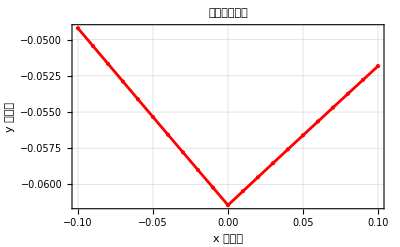

```mathematica
ListPlot[data1,PlotStyle->{Red,PointSize[Medium]},(*散点颜色和大小*)Joined->True,(*是否将点连接成线*)Mesh->All,(*在连线的同时显示原始数据点*)PlotRange->All,(*确保显示所有数据*)Frame->True,(*使用框架模式*)FrameLabel->{"x 轴标签","y 轴标签"},(*设置坐标轴名称*)PlotLabel->"数据图表标题",(*图表标题*)GridLines->Automatic                 (*添加网格线*)]
```

```mathematica
result2 = calcFunc[#]&/@Δrlists
data1 = Transpose[{Δrlists,result2}]
ListPlot[data1,PlotStyle->{Red,PointSize[Medium]},(*散点颜色和大小*)Joined->True,(*是否将点连接成线*)Mesh->All,(*在连线的同时显示原始数据点*)PlotRange->All,(*确保显示所有数据*)Frame->True,(*使用框架模式*)FrameLabel->{"x 轴标签","y 轴标签"},(*设置坐标轴名称*)PlotLabel->"数据图表标题",(*图表标题*)GridLines->Automatic                 (*添加网格线*)]
```

{-0.0492098,-0.0504395,-0.0516677,-0.0528946,-0.0541199,-0.0553437,-0.0565658,-0.0577861,-0.0590046,-0.0602212,-0.0614357,-0.060467,-0.0594999,-0.0585345,-0.0575708,-0.0566088,-0.0556485,-0.0546899,-0.0537332,-0.0527782,-0.051825}

{{-0.1,-0.0492098},{-0.09,-0.0504395},{-0.08,-0.0516677},{-0.07,-0.0528946},{-0.06,-0.0541199},{-0.05,-0.0553437},{-0.04,-0.0565658},{-0.03,-0.0577861},{-0.02,-0.0590046},{-0.01,-0.0602212},{0.,-0.0614357},{0.01,-0.060467},{0.02,-0.0594999},{0.03,-0.0585345},{0.04,-0.0575708},{0.05,-0.0566088},{0.06,-0.0556485},{0.07,-0.0546899},{0.08,-0.0537332},{0.09,-0.0527782},{0.1,-0.051825}}

-Graphics-

```mathematica
epsl = 10^-6;
N[r/(√2) h2lm/.parametersvalue/.{Δr->{-epsl,0,epsl},M->1,B[i_,j_]->Beta[i,j],F[i_,j_,k_,l_]->Hypergeometric2F1[i,j,k,l]}]
```

{-0.627148+1.08945 ⅈ,-0.614357+1.0641 ⅈ,-0.601566+1.03875 ⅈ}

## (ψ^P)_(l, m) (t, r)

```mathematica
ψP[t_,r_,l_,m_,ℰ_,ℒ_,r0_,ϕ0_,Δr_]:=2 ⅇ^(ⅈ m ((r0 ur ℒ Δr)/((-2 M+r0) (r0^2+ℒ^2))-ϕ0)) √(1/(1+2 l)) √π r ((((1+2 l)^2 r0^2 ℰ^2 Δr^2 EllipticE[ℒ^2/(r0^2+ℒ^2)])/(4 π (-2 M+r0)^2 (r0^2+ℒ^2)^(3/2))+(2 EllipticK[ℒ^2/(r0^2+ℒ^2)])/(π √(r0^2+ℒ^2))+((-1+2 l) (1+2 l)^2 (3+2 l) r0^4 ℰ^4 Δr^4 (2 (2 r0^2+ℒ^2) EllipticE[ℒ^2/(r0^2+ℒ^2)]-r0^2 EllipticK[ℒ^2/(r0^2+ℒ^2)]))/(576 π (-2 M+r0)^4 (r0^2+ℒ^2)^(7/2))+Δr (-((1+2 l) r0 ℰ)/(2 (-2 M+r0) (r0^2+ℒ^2))-(l (1+l) (1+2 l) r0^3 ℰ^3 (2 r0^2+ℒ^2) Δr^2)/(24 (-2 M+r0)^3 (r0^2+ℒ^2)^3)) Sign[Δr]) WignerD[{l,m,0},π,π/2,π/2]+((Δr ((r0^2 (4 M-r0 (2-3 ℰ^2)) ℒ+(4 M-2 r0) ℒ^3) EllipticE[ℒ^2/(r0^2+ℒ^2)]-2 r0^3 ℰ^2 ℒ EllipticK[ℒ^2/(r0^2+ℒ^2)]))/(π r0 (-2 M+r0) ℒ (r0^2+ℒ^2)^(3/2))-1/(8 π (-2 M+r0)^3 ℒ (r0^2+ℒ^2)^(7/2))(1+2 l)^2 r0 Δr^3 (2 (r0^3 ℰ^4 ℒ (-3 r0^2+ℒ^2)+ℰ^2 ℒ (r0^2+ℒ^2) (r0^2 (-7 M+4 r0)+(-M+r0) ℒ^2)) EllipticE[ℒ^2/(r0^2+ℒ^2)]+r0^2 ℰ^2 (r0^2 (4 M-r0 (2-3 ℰ^2)) ℒ+(4 M-2 r0) ℒ^3) EllipticK[ℒ^2/(r0^2+ℒ^2)])+Δr (((1+2 l) (2 r0^3 ℰ^4 (-r0+ℒ) (r0+ℒ)+ℰ^2 (r0^2+ℒ^2) (r0^2 (-7 M+4 r0)+(-M+r0) ℒ^2)) Δr)/(4 (-2 M+r0)^2 ℰ (r0^2+ℒ^2)^3)+1/(48 (-2 M+r0)^4 (r0^2+ℒ^2)^5)l (1+l) (1+2 l) r0^2 ℰ (2 r0^3 ℰ^4 (-4 r0^4+3 r0^2 ℒ^2+ℒ^4)+ℰ^2 (r0^2+ℒ^2) (2 r0^4 (-13 M+8 r0)+r0^2 (-11 M+10 r0) ℒ^2+3 (-M+r0) ℒ^4)) Δr^3) Sign[Δr]) WignerD[{l,m,0},π,π/2,π/2]+√(l (1+l)) ((4 r0 ur (EllipticE[ℒ^2/(r0^2+ℒ^2)]-EllipticK[ℒ^2/(r0^2+ℒ^2)]))/((-1+2 l) (3+2 l) π ℒ √(r0^2+ℒ^2))-1/(2 π (-2 M+r0)^2 ℒ^2 (r0^2+ℒ^2)^(5/2))Δr^2 (ur ℒ (r0^4 (6 M+r0 (-4+5 ℰ^2))-r0^2 (-8 M+r0 (6+3 ℰ^2)) ℒ^2+2 (M-r0) ℒ^4) EllipticE[ℒ^2/(r0^2+ℒ^2)]+ur ℒ (r0^4 (-6 M+r0 (4-5 ℰ^2))+2 r0^2 (-4 M+r0 (3+ℰ^2)) ℒ^2+2 (-M+r0) ℒ^4) EllipticK[ℒ^2/(r0^2+ℒ^2)])+1/(96 π (-2 M+r0)^4 ℒ^2 (r0^2+ℒ^2)^(9/2))(1+2 l)^2 r0^2 ℰ^2 Δr^4 (ur ℒ (r0^6 (-12 M+r0 (8-11 ℰ^2))+r0^4 (-4 M+4 r0+19 r0 ℰ^2) ℒ^2-2 r0^2 (-6 M+r0 (4+ℰ^2)) ℒ^4+4 (M-r0) ℒ^6) EllipticE[ℒ^2/(r0^2+ℒ^2)]-r0^2 ur ℒ (r0^4 (-12 M+r0 (8-11 ℰ^2))+r0^2 (-16 M+r0 (12+5 ℰ^2)) ℒ^2+4 (-M+r0) ℒ^4) EllipticK[ℒ^2/(r0^2+ℒ^2)])+1/(24 (-2 M+r0)^3 (r0^2+ℒ^2)^4)(1+2 l) r0 ur ℰ ℒ (r0^4 (-9 M+2 r0 (3-5 ℰ^2))+r0^2 (-12 M+r0 (9+2 ℰ^2)) ℒ^2+3 (-M+r0) ℒ^4) Δr^3 Sign[Δr]) (-WignerD[{l,m,-1},π,π/2,π/2]+WignerD[{l,m,1},π,π/2,π/2])+√((-1+l) l (1+l) (2+l)) (((1+3/((-1+2 l) (3+2 l))) ℰ^2 Δr^2 (r0^2 (2 r0^2+ℒ^2) EllipticE[ℒ^2/(r0^2+ℒ^2)]-2 r0^4 EllipticK[ℒ^2/(r0^2+ℒ^2)]))/(3 π (-2 M+r0)^2 ℒ^2 (r0^2+ℒ^2)^(3/2))+1/(π ℒ^2 √(r0^2+ℒ^2))8 (1/((-1+2 l) (3+2 l))+3/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) (2 (r0^2+ℒ^2) EllipticE[ℒ^2/(r0^2+ℒ^2)]-(2 r0^2+ℒ^2) EllipticK[ℒ^2/(r0^2+ℒ^2)])-((5-(1+2 l)^2) r0^4 ℰ^4 Δr^4 (2 (r0^4+r0^2 ℒ^2+ℒ^4) EllipticE[ℒ^2/(r0^2+ℒ^2)]-r0^2 (2 r0^2+ℒ^2) EllipticK[ℒ^2/(r0^2+ℒ^2)]))/(240 π (-2 M+r0)^4 ℒ^2 (r0^2+ℒ^2)^(7/2))-((1+2 l) r0^3 ℰ^3 ℒ^2 Δr^3 Sign[Δr])/(48 (-2 M+r0)^3 (r0^2+ℒ^2)^3)) (WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2])+√((-1+l) l (1+l) (2+l)) (-1/(π r0 (-2 M+r0) ℒ^3 (r0^2+ℒ^2)^(3/2))4 (1/((-1+2 l) (3+2 l))+3/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) Δr (ℒ (-2 r0^4 (-4 M+r0 (2-5 ℰ^2))+r0^2 (12 M+r0 (-6+7 ℰ^2)) ℒ^2+(4 M-2 r0) ℒ^4) EllipticE[ℒ^2/(r0^2+ℒ^2)]+2 r0^2 (r0^2 (-4 M+r0 (2-5 ℰ^2)) ℒ+(-4 M+r0 (2-ℰ^2)) ℒ^3) EllipticK[ℒ^2/(r0^2+ℒ^2)])-1/(6 π (-2 M+r0)^3 ℒ^3 (r0^2+ℒ^2)^(7/2))(1+3/((-1+2 l) (3+2 l))) r0 Δr^3 (2 (r0^3 ℰ^4 ℒ (3 r0^4+8 r0^2 ℒ^2+ℒ^4)+ℰ^2 ℒ (r0^2+ℒ^2) (r0^4 (-2 M+2 r0)+3 M r0^2 ℒ^2+(-M+r0) ℒ^4)) EllipticE[ℒ^2/(r0^2+ℒ^2)]+r0^2 (ℰ^2 ℒ (r0^2+ℒ^2) (-2 r0^2 (-2 M+2 r0)+(-8 M+2 r0) ℒ^2)-ℰ^4 (6 r0^5 ℒ+13 r0^3 ℒ^3)) EllipticK[ℒ^2/(r0^2+ℒ^2)])+1/(96 (-2 M+r0)^4 (r0^2+ℒ^2)^5)(1+2 l) r0^2 ℰ ℒ (2 r0^3 ℰ^4 ℒ (-5 r0^2+ℒ^2)+3 ℰ^2 ℒ (r0^2+ℒ^2) (r0^2 (-7 M+4 r0)+(-M+r0) ℒ^2)) Δr^4 Sign[Δr]) (WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2]));
```

```mathematica
Re[ψP[0,r0value+Δr,l,m,ℰ,ℒ,r0,ϕ0,Δr]/.parametersvalue/.{Δr->Δrlists,M->1}]
```

{0.460404,0.4619,0.463399,0.464901,0.466405,0.467912,0.469422,0.470935,0.472451,0.473969,0.47549,0.474475,0.473463,0.472454,0.471448,0.470445,0.469445,0.468449,0.467455,0.466465,0.465477}

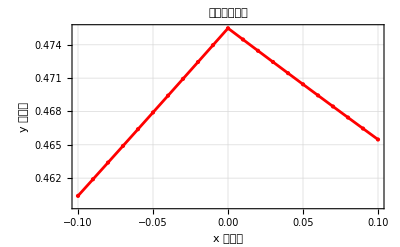

```mathematica
data2 = Transpose[{Δrlists,%}];
ListPlot[data2,PlotStyle->{Red,PointSize[Medium]},(*散点颜色和大小*)Joined->True,(*是否将点连接成线*)Mesh->All,(*在连线的同时显示原始数据点*)PlotRange->All,(*确保显示所有数据*)Frame->True,(*使用框架模式*)FrameLabel->{"x 轴标签","y 轴标签"},(*设置坐标轴名称*)PlotLabel->"数据图表标题",(*图表标题*)GridLines->Automatic                 (*添加网格线*)]
```

```mathematica
Sign[Δrlists]
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,1,1,1,1,1,1,1,1,1,1}

ψP[0.,{9.9,9.91,9.92,9.93,9.94,9.95,9.96,9.97,9.98,9.99,10.,10.01,10.02,10.03,10.04,10.05,10.06,10.07,10.08,10.09,10.1},2.,2.,0.956969,3.78517,10.,0.523599,{-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}]

```mathematica
ψP[0,r,lvalue,mvalue,ℰvalue,ℒvalue,r0value,ϕ0value,Δr]
```

ψP[0,r,2,2,√(87/95),(35 √(2/19))/3,10,π/6,Δr]

```mathematica
Plot[ψP[0,r0value+Δr,lvalue,mvalue,ℰvalue,ℒvalue,r0value,ϕ0value,Δr]/.parametersvalue,{Δr,-0.1,0.1}]
```

-Graphics-

## 检查

```mathematica
Il
```

{{((1+2 l) (-2 M+r0) (L^2+r0^2) Δr^2 F[1,1/2,1,k])/(2 r0^2 ℰ (r0^2+ℒ^2)^(3/2))-((1+2 l)^2 Δr^3 F[3/2,1/2,1,k])/(4 (r0^2+ℒ^2)^(3/2))+(l (1+3 l+2 l^2) r0^2 ℰ Δr^4 F[2,1/2,1,k])/(4 (-2 M+r0) (L^2+r0^2) (r0^2+ℒ^2)^(3/2)),-(c (1+2 l) (-2 M+r0) (L^2+r0^2) Δr^2 F[1,1/2,1,k])/(2 r0^2 ℰ (r0^2+ℒ^2)^(3/2))+(c (1+2 l)^2 Δr^3 F[3/2,1/2,1,k])/(4 (r0^2+ℒ^2)^(3/2))-(c l (1+3 l+2 l^2) r0^2 ℰ Δr^4 F[2,1/2,1,k])/(4 (-2 M+r0) (L^2+r0^2) (r0^2+ℒ^2)^(3/2)),(Δr B[3/2,1/2] F[3/2,3/2,2,k])/(π (r0^2+ℒ^2)^(3/2))-((1+2 l) r0^2 ℰ Δr^2 B[3/2,1/2] F[2,3/2,2,k])/(π (-2 M+r0) (L^2+r0^2) (r0^2+ℒ^2)^(3/2))+(r0^4 (ℰ+2 l ℰ)^2 Δr^3 B[3/2,1/2] F[5/2,3/2,2,k])/(4 π (-2 M+r0)^2 (L^2+r0^2)^2 (r0^2+ℒ^2)^(3/2))-(l (1+3 l+2 l^2) r0^6 ℰ^3 Δr^4 B[3/2,1/2] F[3,3/2,2,k])/(4 π (-2 M+r0)^3 (L^2+r0^2)^3 (r0^2+ℒ^2)^(3/2)),(Δr B[1/2,3/2] F[3/2,1/2,2,k])/(π (r0^2+ℒ^2)^(3/2))+((1+2 l) Δr^2 (c^2 π (-2 M+r0)^2 (L^2+r0^2)^2 F[1,1/2,1,k]-2 r0^4 ℰ^2 B[1/2,3/2] F[2,1/2,2,k]))/(2 π r0^2 (-2 M+r0) (L^2+r0^2) ℰ (r0^2+ℒ^2)^(3/2))+(Δr^3 (-(c+2 c l)^2 π F[3/2,1/2,1,k]+(r0^4 (ℰ+2 l ℰ)^2 B[1/2,3/2] F[5/2,1/2,2,k])/((-2 M+r0)^2 (L^2+r0^2)^2)))/(4 π (r0^2+ℒ^2)^(3/2))+(l r0^2 ℰ Δr^4 (c^2 π (-2 M+r0)^2 (L^2+r0^2)^2 F[2,1/2,1,k]+3 c^2 l π (-2 M+r0)^2 (L^2+r0^2)^2 F[2,1/2,1,k]+2 c^2 l^2 π (-2 M+r0)^2 (L^2+r0^2)^2 F[2,1/2,1,k]-r0^4 ℰ^2 B[1/2,3/2] F[3,1/2,2,k]-3 l r0^4 ℰ^2 B[1/2,3/2] F[3,1/2,2,k]-2 l^2 r0^4 ℰ^2 B[1/2,3/2] F[3,1/2,2,k]))/(4 π (-2 M+r0)^3 (L^2+r0^2)^3 (r0^2+ℒ^2)^(3/2)),-(c Δr B[3/2,1/2] F[3/2,3/2,2,k])/(π (r0^2+ℒ^2)^(3/2))+(c (1+2 l) r0^2 ℰ Δr^2 B[3/2,1/2] F[2,3/2,2,k])/(π (-2 M+r0) (L^2+r0^2) (r0^2+ℒ^2)^(3/2))-(c r0^4 (ℰ+2 l ℰ)^2 Δr^3 B[3/2,1/2] F[5/2,3/2,2,k])/(4 π (-2 M+r0)^2 (L^2+r0^2)^2 (r0^2+ℒ^2)^(3/2))+(c l (1+3 l+2 l^2) r0^6 ℰ^3 Δr^4 B[3/2,1/2] F[3,3/2,2,k])/(4 π (-2 M+r0)^3 (L^2+r0^2)^3 (r0^2+ℒ^2)^(3/2)),-(3 c Δr B[1/2,3/2] F[3/2,1/2,2,k])/(π (r0^2+ℒ^2)^(3/2))-(c (1+2 l) Δr^2 (c^2 π (-2 M+r0)^2 (L^2+r0^2)^2 F[1,1/2,1,k]-6 r0^4 ℰ^2 B[1/2,3/2] F[2,1/2,2,k]))/(2 π r0^2 (-2 M+r0) (L^2+r0^2) ℰ (r0^2+ℒ^2)^(3/2))+(c Δr^3 ((c+2 c l)^2 π F[3/2,1/2,1,k]-(3 r0^4 (ℰ+2 l ℰ)^2 B[1/2,3/2] F[5/2,1/2,2,k])/((-2 M+r0)^2 (L^2+r0^2)^2)))/(4 π (r0^2+ℒ^2)^(3/2))+(c l r0^2 ℰ Δr^4 (-c^2 π (-2 M+r0)^2 (L^2+r0^2)^2 F[2,1/2,1,k]-3 c^2 l π (-2 M+r0)^2 (L^2+r0^2)^2 F[2,1/2,1,k]-2 c^2 l^2 π (-2 M+r0)^2 (L^2+r0^2)^2 F[2,1/2,1,k]+3 r0^4 ℰ^2 B[1/2,3/2] F[3,1/2,2,k]+9 l r0^4 ℰ^2 B[1/2,3/2] F[3,1/2,2,k]+6 l^2 r0^4 ℰ^2 B[1/2,3/2] F[3,1/2,2,k]))/(4 π (-2 M+r0)^3 (L^2+r0^2)^3 (r0^2+ℒ^2)^(3/2))}}